```mathematica
NS["study_overlearningsimple_generate1"]
```

```mathematica
(* coords transfs to plot the two-distribution space *)
```

```mathematica
trmatrix=T[{{1,0},{0,0},{1/2,Sqrt[3]/2}}];proj[p_]:=trmatrix.p;

plotfreqs[freqs_]:=Block[{nfreqs=(#/Total@#)&@Flatten@freqs},Graphics[{{PointSize@Large,red,Point[proj@nfreqs]}}]];
plotcfreqs[freqs_]:=Block[{nfreqs=(#/Total@#)&@Flatten@freqs},Graphics[{{Thick,red,Circle[proj@nfreqs,0.02]}}]];
sp1={Black,Thin,Line[T[trmatrix][[{1,2,3,1}]]]};
```

```mathematica
(* algorithm to predict & update from data *)
```

```mathematica
(* parametric model *)
expsum[t_]=Table[(1+10*KroneckerDelta[s,1])*Exp[t*s],{s,{0,2,1}}];
z[t_]=Total@expsum[t];
prob[t_]=Simplify[expsum[t]/z[t]]
```

{1/(1+11 ⅇ^t+ⅇ^(2 t)),ⅇ^(2 t)/(1+11 ⅇ^t+ⅇ^(2 t)),(11 ⅇ^t)/(1+11 ⅇ^t+ⅇ^(2 t))}

```mathematica
priort[t_,m_,s_]:=(PDF[NormalDistribution[m,s],t]+PDF[NormalDistribution[-m,s],t])/2;
```

```mathematica
(* representation of parameter density on simplex *)
```

```mathematica
tran[t_]=FS[prob[t][[3]]]
```

1/(1+(2 Cosh[t])/11)

```mathematica
somax=prob[0][[3]]
```

11/13

```mathematica
dpdt[t_]=Assuming[Element[t,Reals],FullSimplify[Abs@D[tran[t],t]]]
```

(22 Abs[Sinh[t]])/(11+2 Cosh[t])^2

```mathematica
inve[so_]=t/.Flatten[Assuming[0<so<somax,FS@Solve[so==tran[t],t,Reals]]]
```

-ArcCosh[-(11 (-1+so))/(2 so)]

```mathematica
Plot[inve[so],{so,0,somax}]
```

```mathematica
dens[so_,mx_,sx_]=2*Assuming[0<so<somax,Simplify@priort[inve[so],mx,sx]/dpdt[inve[so]]]
```

((ⅇ^(-(mx-ArcCosh[-(11 (-1+so))/(2 so)])^2/(2 sx^2))+ⅇ^(-(mx+ArcCosh[-(11 (-1+so))/(2 so)])^2/(2 sx^2))) (11-(11 (-1+so))/so)^2)/(22 √(2 π) sx Abs[√((-1-(11 (-1+so))/(2 so))/(1-(11 (-1+so))/(2 so))) (1-(11 (-1+so))/(2 so))])

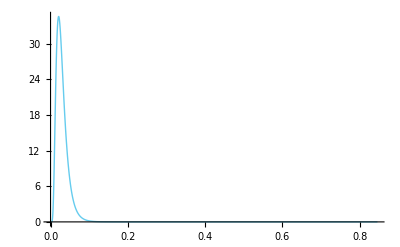

```mathematica
Plot[dens[so,6,1/2],{so,0,somax},PlotRange->All]
```

```mathematica
Limit[dens[so,6,1/2],so->somax]
```

∞

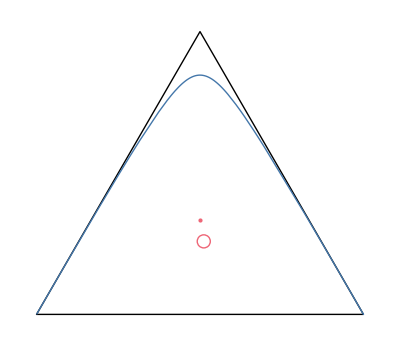

```mathematica
rfreqs=Flatten@{{{1/2,1/2}*2/3,1/3}};

samples=100;
data=RandomChoice[rfreqs->Range[3],samples];

rfreqs0=(#/Total@#)&@(Count[data,#]&/@{1,2,3});


ppplot1=ParametricPlot[proj@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,purpleblue}];
ddoms={Graphics[{sp1}],ppplot1};
Show[{ddoms,plotfreqs@rfreqs,plotcfreqs@rfreqs0},PlotRange->All]
```

```mathematica
ProgressIndicator[Dynamic[i],{0,samples}]
```

```mathematica
samples=Length[data];m=6;s=1/2;freqs=Table[0,{3}];evidence=1;
probh=Table[Null,{samples}];
surph=Table[Null,{samples}];
logev=Table[Null,{samples}];

Do[(*Print[i];Print[freqs];*)

integral=
NIntegrate[prob[t]*Times@@(prob[t]^freqs)*priort[t,m,s],{t,-Infinity,+Infinity}];
(*Print[{i,integral//MF}];*)
probh[[i]]=integral/evidence;
(*Print[integral];Print[probh[[i]]];Print[data[[i]]];*)
surph[[i]]=-Log[probh[[i,data[[i]]]]];

evidence=integral[[data[[i]]]];
logev[[i]]=Log[evidence];
++freqs[[data[[i]]]];
,{i,samples}]
```

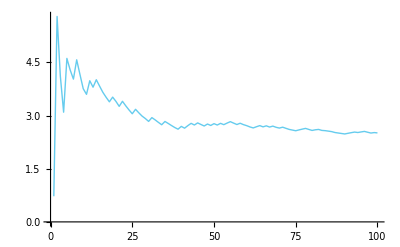

```mathematica
ListPlot[-logev/Range[samples],Joined->True,PlotRange->All]
```

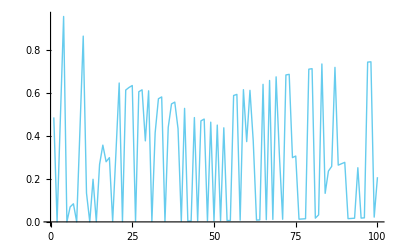

```mathematica
ListPlot[Exp@-surph,Joined->True,PlotRange->All]
```

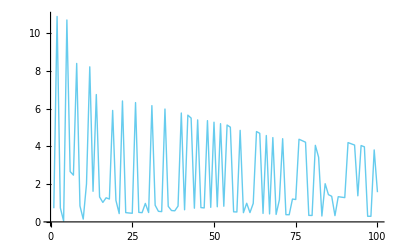

```mathematica
ListPlot[surph,Joined->True,PlotRange->All]
```

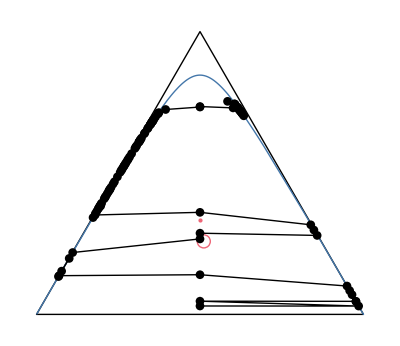

```mathematica
subrange=Round[Range[1,samples,samples/samples]];rplot1=ListPlot[Table[proj@probh[[i]],{i,subrange}],Axes->None,PlotRange->All,PlotStyle->Black,Joined->True,PlotMarkers->Auto];
Show[{ddoms,plotfreqs@rfreqs,plotcfreqs@freqs,rplot1},PlotRange->All]
```

```mathematica
entropy[p_]:=Block[{xlogx},
xlogx[x_]:=If[x>0,x*Log[x],0];
SetAttributes[xlogx,Listable];
Total@xlogx[p]];
```

```mathematica
(Exp@-entropy[rfreqs])^10*2
```

118098

```mathematica
rfreqs
```

{1/3,1/3,1/3}